```mathematica
DSolve[{x y'[x]==x^2 Cos[x],y[0]==0},y[x],x]
```

{{y[x]→-1+Cos[x]+x Sin[x]}}

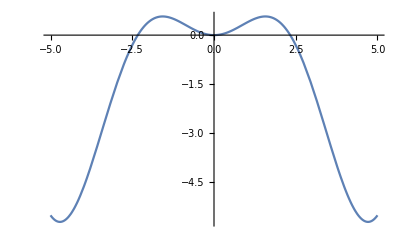

```mathematica
Plot[-1+Cos[x]+x Sin[x], {x, -5,5}]
```

```mathematica
DSolve[{y''[x]+y[x]==0,y[0]==1, y'[0]==-0.5},y[x],x]
```

{{y[x]→Cos[x]-0.5 Sin[x]}}

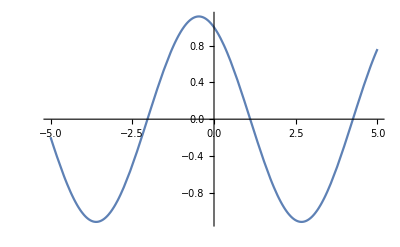

```mathematica
Plot[Cos[x]-0.5 Sin[x], {x, -5,5}]
```

```mathematica
Solve[3*Sin[π*x]==0, x]
```

{{x→ConditionalExpression[2 C[1], C[1]∈ℤ]},{x→ConditionalExpression[(π+2 π C[1])/π, C[1]∈ℤ]}}

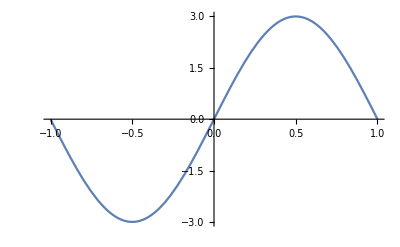

```mathematica
Plot[3*Sin[π*x], {x,-1,1}]
```

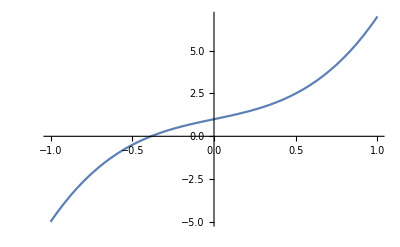

```mathematica
Plot[1+2x+4x^3, {x,-1,1}]
```

```mathematica
Solve[1+2x+4x^3==0, x]
```

{{x→Root-0.385Root[1+2 #1+4 #1^3&,1]-0.385458498529624},{x→Root0.193-0.782 ⅈRoot[1+2 #1+4 #1^3&,2]0.19272924926481205},{x→Root0.193+0.782 ⅈRoot[1+2 #1+4 #1^3&,3]0.19272924926481205}}